```mathematica
levelNames ={"a1","a2","b1","b2"};
```

```mathematica
rootPath = NotebookDirectory[];
```

```mathematica
texts = Table[Import[ FileNameJoin[{rootPath , "data","sentences" ,StringJoin[ level," sentences.txt"]}]],{level,levelNames}];
```

```mathematica
TextSentences[texts[[1]],4] (*Show 4 sentences, only A1 level*)
```

{I would like that, my dear.,I would like to order  la carte.,I would like to compose a message.,Beautiful work.}

```mathematica
Flatten[TextSentences[#,1]&@texts](*Show 1 sentence, all levels in one array*)
```

{I would like that, my dear.,That’s Speedy!,And guess what?,He couldn't even guess.}

```mathematica
sentencesFull=Map[Select[StringSplit[#,"\n"],StringLength[#]>=2&]&,texts];
```

```mathematica
nSents =All;(*reduce number of sentences if too slow*)
```

```mathematica
sentences= Map[Take[#,nSents]&,sentencesFull];
```

```mathematica
nameLength={levelNames,Map[Length,sentences]}ᵀ;nameLength//TableForm
```

a1 | 2000
a2 | 2000
b1 | 2000
b2 | 2000

```mathematica
labels=Flatten[Table[Table[x[[1]],x[[2]]],{x,nameLength}]];
```

```mathematica
embedding=NetModel["GloVe 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"]
```

EmbeddingLayer[<>]

```mathematica
decoder=NetDecoder[{"Class",levelNames}]
```

NetDecoder[<>]

```mathematica
encoder = NetEncoder[decoder];
```

```mathematica
encodedLabels=Thread[UnitVector[Length[levelNames],encoder[labels]]];
Dimensions[encodedLabels]
RandomSample[{labels,encodedLabels}ᵀ,4]//TraditionalForm
```

{8000,4}

(a2 | {0,1,0,0}
a2 | {0,1,0,0}
a2 | {0,1,0,0}
a2 | {0,1,0,0})

```mathematica
encodedWords=embedding[Flatten[sentences]];
```

```mathematica
encodedSentences=Map[Mean,encodedWords];
Dimensions[encodedSentences]
```

{8000,50}

```mathematica
allData=Thread[encodedSentences->encodedLabels];allData[[1]]
```

{0.214019,0.271261,0.0504771,-0.276674,0.502119,0.0583472,-0.400325,-0.0207804,-0.278395,0.0111262,-0.100528,0.618868,-0.417139,-0.137525,0.651601,0.404062,-0.005945,0.105084,0.130525,-0.439414,-0.228674,0.428292,0.379462,0.0416915,0.528543,-1.73525,-0.789228,0.155749,0.446609,-0.553966,2.80366,0.391172,-0.386574,-0.00050975,-0.116356,-0.154927,0.13208,0.0334483,0.321645,-0.272565,-0.109711,0.119482,-0.138774,0.242132,0.157917,0.140987,-0.210705,-0.206912,-0.0672505,0.348317}→{1,0,0,0}

```mathematica
trainingData = RandomSample[allData,Round[0.7Length[allData]]];
```

```mathematica
testingData=Complement[allData,trainingData];
```

```mathematica
(*untrainedClassifier=NetChain[{LinearLayer[]},"Input"->50,"Output"->decoder]*)
```

```mathematica
(*trainedClassifier=NetTrain[untrainedClassifier,trainingData]*)
```

```mathematica
decoder[Values[trainingData]];
```

```mathematica
trainedClassifier=Classify[Keys[trainingData]->decoder[Values[trainingData]],Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[trainedClassifier]
```

Classifier information
Method | Neural network
Number of classes | 4
Number of features | 1
Number of training examples | 5600
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,150150
Hidden layer activation functions | ,,Rectified LinearRectified Linear
CostFunction | Cost Function

```mathematica
Keys[testingData[[2]]]
```

{-0.36736,0.483816,-0.108016,0.180247,0.444224,0.295615,-0.457015,0.232307,-0.302064,-0.134883,-0.130839,-0.123798,-0.777888,-0.157678,0.77288,-0.172833,0.087615,-0.195933,-0.792857,-0.26874,0.0532933,0.148876,0.243797,0.0537292,0.140993,-1.53625,-0.358448,-0.0852768,0.085525,-0.225983,2.65934,0.329926,-0.356735,-0.0637383,-0.0644477,-0.023065,0.296738,0.650165,-0.0432744,-0.588276,0.146753,-0.011443,-0.172931,-0.109315,-0.405292,0.122938,-0.201929,-0.492838,0.243559,-0.20182}

```mathematica
trainedClassifier[Keys[testingData[[2]]]]
```

a1

```mathematica
cm=ClassifierMeasurements[trainedClassifier,Keys[testingData]->decoder[Values[testingData]]]
```

ClassifierMeasurementsObject[…]

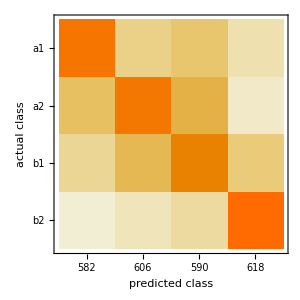

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

0.722871

```mathematica
props=cm["Properties"];
```

```mathematica
cm["TopConfusions"]
```

{a2→b1,a1→b1,b1→b2,a1→a2,a1→b2,a2→b2}